## SimulateHPLC: Data Generation and Usage

Use the following web site to generate desired chromatogram data. Export the generated data to you computer.

```mathematica
SystemOpen["https://www.multidlc.org/hplcsim/4_0_0/"]
```

Simulation parameters:
Compounds used

Simulation parameters

Compounds: phenol (concentration and 3-phenylpropanol

Injection volume 5 microlitter

Solvent A = water, Solvent B =Acetonitrile

Solvent B fraction: 40% v/v

Gradient: {0 min. 5% B},{5 min. 95% B}

Flow rates: 0.1, 0.2, 0.3, 0.4, 0.5,1,2,5 ml/min

Column temperatures: 30, 40, 50C

etc. etc.

Import data

Add units to imported data and turn it into QuantityArray

Function usage:

Function call:

```mathematica
data=SimulateHPLC[50 Celsius,0.5 Milli Liter/Minute]
```

<|Type→Object[Data,Chromatography],ColumnTemperature→50 °C,FlowRates→{0 min,0.5 mL/min},Absorbance→{{0. min,0 m AbsorbanceUnit},{0.01 min,0 m AbsorbanceUnit},«751»,{6.28 min,2.57002×10^-10 m AbsorbanceUnit},{6.28 min,3.0619×10^-11 m AbsorbanceUnit}}|>

Extract absorbance:

```mathematica
data[Absorbance]
```

Plot

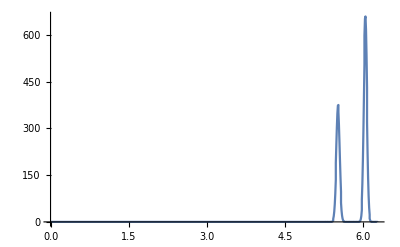

```mathematica
ListLinePlot[data[Absorbance]]
```

Upload to Constellation if desired:

```mathematica
Upload[<|Type->Object[Data,Chromatography],Replace[ColumnTemperature]->data[ColumnTemperature],Replace[FlowRates]->{data[FlowRates]},
		Replace[Absorbance]->data[Absorbance]|>]
```

-Graphics-New objects added to Constellation:{Object[Data,Chromatography,id:dORYzZJa3RXR]}

Object[Data,Chromatography,id:dORYzZJa3RXR]